0.000113942

0.938272

1.7×10^-11

11

22 mProton+mProton^2

0.00029

0.938418

0.0000914836

0.0000914836

0.00729753

0.1101

0.09207

5.×10^-7

0.134977

1.8×10^-7

0.139571

0.00023

0.775293

0.00013

0.782575

0.000016

1.01945

0.00013

0.00862104

0.0008

0.150385

0.000013

0.00427163

49/50

0.000016

0.493669

0.957962

0.000017

0.547867

6.×10^-6

0.000184148

-Graphics3D-

0.01

0.684034

0.01

0.639463

0.5

41.6729

0.726434

0.1

0.0613428

0.02

0.804394

0.228011

0.365469

0.682747

0.134958

0.0419342

-0.210114

0.083331

0.0921419

-0.00881095

28.7374

21.1865

0.005

3.17×10^-6

6.8×10^-7

0.025

2.57×10^-6

3.7×10^-7

0.05

2.6×10^-6

3.3×10^-7

0.075

1.87×10^-6

2.6×10^-7

0.105

1.76×10^-6

2.4×10^-7

0.14

1.63×10^-6

2.2×10^-7

0.18

1.76×10^-6

2.2×10^-7

0.225

1.97×10^-6

2.4×10^-7

0.265

2.×10^-6

3.2×10^-7

0.295

1.07×10^-6

2.8×10^-7

0.335

3.4×10^-7

9.×10^-8

0.39

1.2×10^-7

4.×10^-8

0.53

6.×10^-8

2.×10^-8

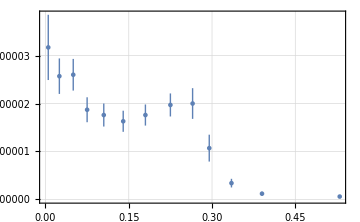

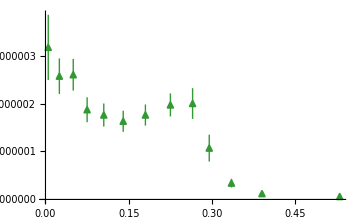

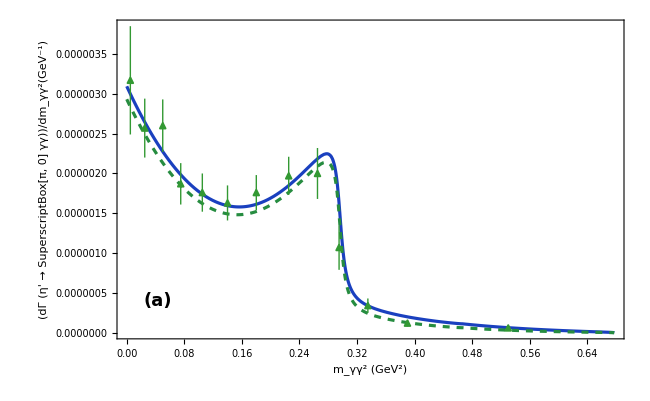

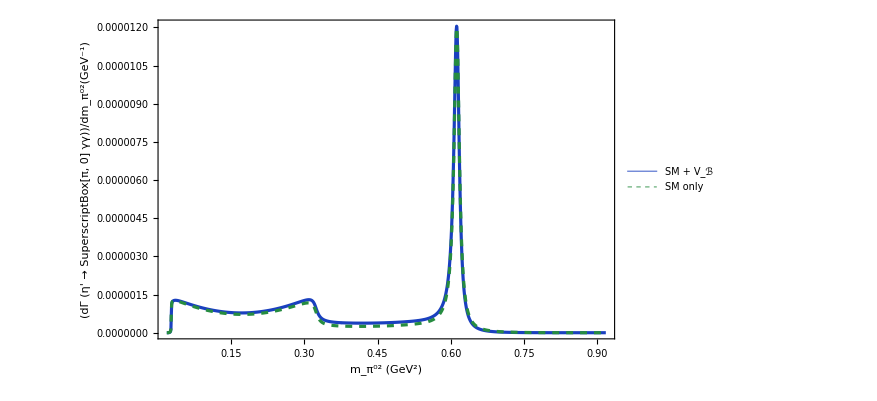

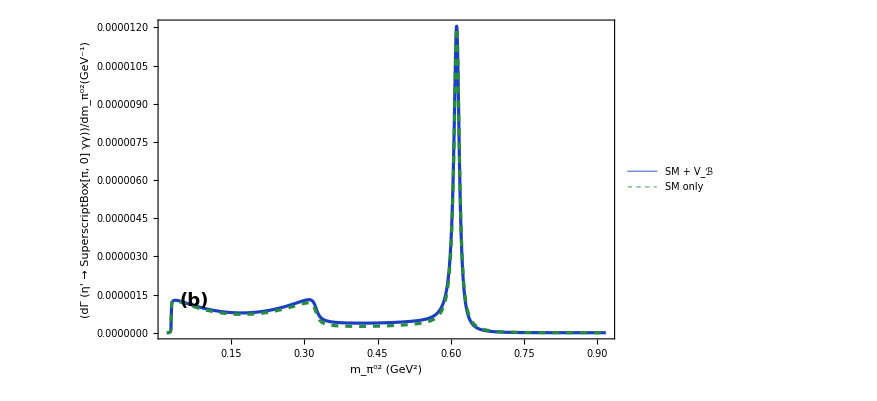

EtaPrimeGammaGammaSpectrumRun1.pdf

EtaPrimePi0GammaSpectrumRun1.pdf

```mathematica
(*Run 1*)
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
CoupleEff = GenerateValue[0.0000853727272727272,0.000010835775045318799]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
Δα=0.000000017*10^(-3)

EnergyPhoton =11
sIncoming = mProton^2+2*mProton*EnergyPhoton
ΔmProton = 0.00029
mProton=GenerateValue[0.93827208943,ΔmProton]
CoupleEff = GenerateValue[0.0000853727272727272,0.000010835775045318799]
BestYukawa2Cs2Ms6MB2=CoupleEff


α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
Δmπ=0.0005*10^(-3)
mπ=GenerateValue[134.9768*10^(-3),Δmπ]
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
MηPrime = GenerateValue[957.78*10^(-3),0.06*10^(-3)]


ΔMη=0.017*10^(-3)
Mη = GenerateValue[547.862*10^(-3),ΔMη]

ΔΓtotal = 0.006*10^(-3)
Γtotal=GenerateValue[0.188*10^(-3),ΔΓtotal]
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-(-(-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-((-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, mπ^2, MηPrime^2},{m232, mπ^2, MηPrime^2}, PlotRange->All]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρπγ = g/3
gρηPγ = g*zNS*Sin[ϕP]

gωπγ = g*Cos[ϕV]
gωηPγ =g/3*(zNS*Sin[ϕP]*Cos[ϕV]+2*zSmBm*Cos[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηPγ =g/3*(zNS*Sin[ϕP]*Sin[ϕV]-2*zSmBm*Cos[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηPγ
cω = gωπγ*gωηPγ
cϕ = gϕπγ*gϕηPγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]


MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq1Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]

βPlusπη[s_]:=√(1-(Mη+mπ)^2/s)
βMinusπη[s_]:=√(1-(Mη-mπ)^2/s)
βBarPlusπη[s_]:=√(-1+(Mη+mπ)^2/s)
βBarMinusπη[s_]:=√(-1+(-Mη+mπ)^2/s)
θπη[s_]:= HeavisideTheta[-(Mη+mπ)^2+s]
Barθπη[s_]:= HeavisideTheta[(Mη+mπ)^2-s]*HeavisideTheta[-(-Mη+mπ)^2+s]
BarBarθπη[s_]:= HeavisideTheta[(-Mη+mπ)^2-s]


ga0πηSq=((-maZero^2+Mη^2)^2 Cos[ϕP]^2)/fπ^2

βK[s_]:=√(1-(4*mKP^2)/s)
βKbar[s_]:=√((4*mKP^2)/s-1)
θK[s_]:= HeavisideTheta[-4*mKP^2+s]
θKbar[s_]:= HeavisideTheta[4*mKP^2-s]
ga0KKbarSq=((-maZero^2+mKP^2)^2)/(2 fK^2)
R1[s_]:=ga0KKbarSq/(16 π^2)*(2-Log[(1+βK[s])/(1-βK[s])] *βK[s]* θK[s]-2 ArcTan[1/βKbar[s]]* βKbar[s]* θKbar[s])

R2[s_]:=ga0πηSq/(16 π^2)*(2-((Mη^2-mπ^2) *Log[Mη/mπ])/s-Log[(βMinusπη[s]+βPlusπη[s])/(βMinusπη[s]-βPlusπη[s])]* βMinusπη[s]* βPlusπη[s]* θπη[s])

R3[s_]:=ga0πηSq/(16 π^2)*(BarBarθπη[s]*Log[(βBarMinusπη[s]+βBarPlusπη[s])/(-βBarMinusπη[s]+βBarPlusπη[s])]*βBarMinusπη[s]*βBarPlusπη[s]-2*ArcTan[βMinusπη[s]/βBarPlusπη[s]]*Barθπη[s]*βBarPlusπη[s]*βMinusπη[s])

ImaginaryPart[s_]:=-(ga0KKbarSq* βK[s]* θK[s])/(16 π)-(ga0πηSq* βPlusπη[s]* βMinusπη[s]*θπη[s])/(16 π)

R[s_]:=R1[s]+R2[s]+R3[s]

Da0[s_]:=-maZero^2+s+R[s]-R[maZero^2]+I*ImaginaryPart[s]
ALSM[s_]:=1/(2*fK*fπ)*((-MηPrime^2+s)*((-maZero^2+mKP^2)/Da0[s])*Sin[ϕP]+1/6 ((5 MηPrime^2+mπ^2-3 s)*Sin[ϕP]+√2*(4 mKP^2+MηPrime^2+mπ^2-3 s)*Cos[ϕP]))
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=(2*(-m132-m232+MηPrime^2+mπ^2)^2*Abs[(α ALSM[-m132-m232+MηPrime^2+mπ^2]* L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2])/mKP^2]^2)/π^2*Constraint[m132, m232]
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMD[m132,MηPrime^2+mπ^2 - m132 - m122]+Interference[m132,MηPrime^2+mπ^2 - m132 - m122]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
p1 = (0.0 + 0.01)/2
v1 = 3.17*10^(-6)
u1 = (0.44 + 0.24)*10^(-6)
p2 = (0.01 + 0.04)/2
v2 = 2.57*10^(-6)
u2 = (0.18+0.19)*10^(-6)
p3 = (0.04 + 0.06)/2
v3 = 2.60*10^(-6)
u3 = (0.15 + 0.18)*10^(-6)
p4  = (0.06 + 0.09)/2
v4 = 1.87*10^(-6)
u4 = (0.12 +0.14)*10^(-6)
p5 = (0.09 + 0.12)/2
v5 = 1.76*10^(-6)
u5 = (0.11 + 0.13)*10^(-6)
p6 = (0.12 + 0.16)/2
v6 = 1.63*10^(-6)
u6 = (0.10 + 0.12)*10^(-6)
p7 = (0.16 + 0.20)/2
v7 = 1.76*10^(-6)
u7 = (0.09 + 0.13)*10^(-6)
p8 = (0.20 + 0.25)/2
v8 = 1.97*10^(-6)
u8 = (0.10 + 0.14)*10^(-6)
p9 = (0.25+0.28)/2
v9 = 2.00*10^(-6)
u9 = (0.17 + 0.15)*10^(-6)
p10 = (0.28 + 0.31)/2
v10 = 1.07*10^(-6)
u10 = (0.20 + 0.08)*10^(-6)
p11 = (0.31 + 0.36)/2
v11 = 0.34*10^(-6)
u11  = (0.06 + 0.03)*10^(-6)
p12 = (0.36 + 0.42)/2
v12 = 0.12 *10^(-6)
u12 = (0.03 + 0.01)*10^(-6)
p13 = (0.42 + 0.64)/2
v13 = 0.06*10^(-6)
u13  = (0.01 + 0.01)*10^(-6)
pExp=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]} ,{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]},{Around[p8,0],Around[v8,u8]},{Around[p9,0],Around[v9,u9]}
,{Around[p10,0],Around[v10,u10]},{Around[p11,0],Around[v11,u11]},{Around[p12,0],Around[v12,u12]}
,{Around[p13,0],Around[v13,u13]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
BWtDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWuDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWtuDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)]

MatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,Yukawa2Cs2Ms6]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,Yukawa2Cs2Ms6] +Bq1Bq1[m132,m232]*BWuDARK[m132,m232,Yukawa2Cs2Ms6])*Constraint[m132, m232]

Int1VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω))]
InterferenceDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=2*Re[Int1VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]*Int2VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,Yukawa2Cs2Ms6_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMDDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6]+InterferenceDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
colBES=RGBColor[0.20,0.60,0.20];
colNP=RGBColor[0.10,0.25,0.75];
colSM=RGBColor[0.15,0.55,0.25];besMarker=Graphics[{EdgeForm[Directive[colBES,AbsoluteThickness[1.4]]],FaceForm[colBES],Polygon[{{0,1.15},{-1,-0.85},{1,-0.85}}]},PlotRange->{{-1.3,1.3},{-1.3,1.3}},ImageSize->16,Background->None];pExpBES=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]},{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]},{Around[p8,0],Around[v8,u8]},{Around[p9,0],Around[v9,u9]},{Around[p10,0],Around[v10,u10]},{Around[p11,0],Around[v11,u11]},{Around[p12,0],Around[v12,u12]},{Around[p13,0],Around[v13,u13]}},PlotStyle->colBES,PlotMarkers->{besMarker,0.024},Joined->False,Background->None,ImageSize->Automatic]
SummaryTheoryEtaP=Plot[{γγSpectrumDARK[m122,CoupleEff],γγSpectrum[m122]},{m122,0,(MηPrime-mπ)^2},PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,Background->White,BaseStyle->Directive[Black,14],LabelStyle->Directive[Black,18],TicksStyle->Directive[Black,14],PlotStyle->{Directive[colNP,Thickness[0.0035]],Directive[colSM,Dashed,Thickness[0.0035]]        (*SM only*)},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/dm_γγ^2(GeV^-1)"},PlotPoints->160,MaxRecursion->3,PerformanceGoal->"Quality",ImageSize->650];legendLinesEtaP=LineLegend[{Directive[colNP,Thickness[0.005]],Directive[colSM,Dashed,Thickness[0.005]]},{"SM + V_ℬ","SM only"},LabelStyle->Directive[Black,16],LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)];legendPointsBES=PointLegend[{colBES},{"BESIII (lepton)"},LegendMarkers->{besMarker},LabelStyle->Directive[Black,16],LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)];
combinedLegendEtaP=Placed[Framed[Column[{legendLinesEtaP,legendPointsBES},Spacings->.6],FrameStyle->Black,Background->White],{0.83,0.78}];
Part1=Show[Legended[Show[SummaryTheoryEtaP,pExpBES,PlotRange->All,Background->White],combinedLegendEtaP],Epilog->{Text[Style["(a)",18,Bold,Black],Scaled[{.08,.12}]]},ImageSize->650]
πγIn[m132_] := NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγIn[m132])
πγDark[m132_,Yukawa2Cs2Ms6_] := NIntegrate[MatrixVMDDARK[m132,m232,Yukawa2Cs2Ms6]+InterferenceDARK[m132,m232,Yukawa2Cs2Ms6]+LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,Yukawa2Cs2Ms6_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγDark[m132,Yukawa2Cs2Ms6])
Part2=Plot[{πγSpectrumDark[m132,CoupleEff],πγSpectrum[m132]},{m132,mπ^2,MηPrime^2},PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,Background->White,BaseStyle->Directive[Black,14],LabelStyle->Directive[Black,18],TicksStyle->Directive[Black,14],PlotStyle->{Directive[colNP,Thickness[0.0035]], Directive[colSM,Dashed,Thickness[0.0035]]},FrameLabel->{"m_(π^0)^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/(dm_(π^0)^2)(GeV^-1)"},PlotLegends->Placed[LineLegend[{Directive[colNP,Thickness[0.0035]],Directive[colSM,Dashed,Thickness[0.0035]]},{"SM + V_ℬ","SM only"},LabelStyle->Directive[Black,16],LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.14,0.875}],PlotPoints->160,MaxRecursion->3,PerformanceGoal->"Quality",ImageSize->650]
Part2=Show[Part2,Epilog->{Text[Style["(b)",18,Bold,Black],Scaled[{.08,.12}]]}]
Export["EtaPrimeGammaGammaSpectrumRun1.pdf",Part1]
Export["EtaPrimePi0GammaSpectrumRun1.pdf",Part2]
```

```mathematica
OnShellMatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,Yukawa2Cs2Ms6MB2]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,Yukawa2Cs2Ms6MB2] +Bq1Bq1[m132,m232]*BWuDARK[m132,m232,Yukawa2Cs2Ms6MB2])*Constraint[m132, m232]

Ω2[Mx_]:=(√((-(mProton-Mx)^2+sIncoming) (-(mProton+Mx)^2+sIncoming)))/(8 π sIncoming)
VBAloneBWtDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
VBAloneBWuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := Abs[Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2
VBAloneBWtuDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_]:=Re[(Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)*Conjugate[(Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)]]

OnShellVBAloneMatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6MB2_] := (Bq2Bq2p[m132,m232]*VBAloneBWtDARK[m132,m232,Yukawa2Cs2Ms6MB2]+2*Bq2Bq1[m132,m232]*VBAloneBWtuDARK[m132,m232,Yukawa2Cs2Ms6MB2] +Bq1Bq1[m132,m232]*VBAloneBWuDARK[m132,m232,Yukawa2Cs2Ms6MB2])*Constraint[m132, m232]

MxCONSTRAINTm232MAX[Mx_,m132_] := ((Mx^2+mπ^2)^2)/(4 m132)-(-(-m132+Mx^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
MxCONSTRAINTm232MIN[Mx_,m132_] := ((Mx^2+mπ^2)^2)/(4 m132)-((-m132+Mx^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2

MxConstraint[Mx_,m132_, m232_]:=HeavisideTheta[MxCONSTRAINTm232MAX[Mx,m132]-m232]*HeavisideTheta[m232-MxCONSTRAINTm232MIN[Mx,m132]]
MxBq2Bq2p[Mx_,m132_,m232_]:=1/8 (m132^2+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
MxBq1Bq1[Mx_,m132_,m232_]:=1/8 (m232^2+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
MxBq2Bq1[Mx_,m132_,m232_]:=1/8 (m132*m232+Mx^4) (-m132-m232+Mx^2+mπ^2)^2 +1/8 (-m132+Mx^2) (-m232+Mx^2) (m132 m232+Mx^2 (m132+m232-Mx^2-2 mπ^2))
ContinuousVBAloneMatrixVMDDARK[Mx_,m132_,m232_,Yukawa2Cs2Ms6MB2_] := (MxBq2Bq2p[Mx,m132,m232]*VBAloneBWtDARK[m132,m232,Yukawa2Cs2Ms6MB2]+2*MxBq2Bq1[Mx,m132,m232]*VBAloneBWtuDARK[m132,m232,Yukawa2Cs2Ms6MB2] +MxBq1Bq1[Mx,m132,m232]*VBAloneBWuDARK[m132,m232,Yukawa2Cs2Ms6MB2])*MxConstraint[Mx,m132, m232]

PartialContinuosΓ[Mx_,Yukawa2Cs2Ms6MB2_]:=(1/2)*1/(256 Mx^3 π^3)*NIntegrate[ContinuousVBAloneMatrixVMDDARK[Mx,m132,m232,Yukawa2Cs2Ms6MB2], {m132, mπ^2, Mx^2}, {m232, mπ^2, Mx^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
OnShellWidthDark = (1/2)*1/(256 MηPrime^3 π^3)*NIntegrate[OnShellMatrixVMDDARK[m132,m232,BestYukawa2Cs2Ms6MB2]+InterferenceDARK[m132,m232,BestYukawa2Cs2Ms6MB2]+LSM[m132,m232]-OnShellVBAloneMatrixVMDDARK[m132,m232,BestYukawa2Cs2Ms6MB2], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
ContinuosWidthDark [ΔCut_,Yukawa2Cs2Ms6MB2_]:=NIntegrate[2*Mx*Ω2[Mx]*(1/2)*1/(256 Mx^3 π^3)*ContinuousVBAloneMatrixVMDDARK[Mx,m132,m232,Yukawa2Cs2Ms6MB2], {m132, mπ^2, (MηPrime+ΔCut)^2}, {m232, mπ^2, (MηPrime+ΔCut)^2} ,{Mx, MηPrime-ΔCut, MηPrime+ΔCut},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[2*Mx*Ω2[Mx],{Mx,  MηPrime-ΔCut, MηPrime+ΔCut}]
BranchingDark50MeV=(OnShellWidthDark+ContinuosWidthDark [50*10^(-3),BestYukawa2Cs2Ms6MB2])/Γtotal
BranchingDark75MeV=(OnShellWidthDark+ContinuosWidthDark [75*10^(-3),BestYukawa2Cs2Ms6MB2])/Γtotal
BranchingDark100MeV=(OnShellWidthDark+ContinuosWidthDark [100*10^(-3),BestYukawa2Cs2Ms6MB2])/Γtotal
```

6.27865×10^-7

0.00345063

0.00345263

0.00345558

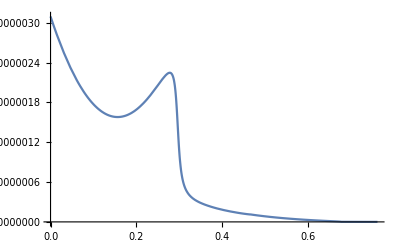

0.958088

0.9582

0.958384

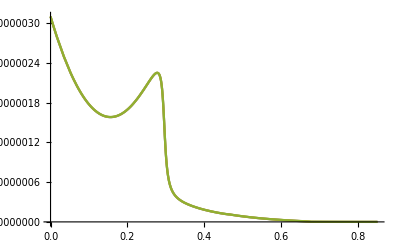

```mathematica
ClearAll[γγSpectrumDARK];
γγSpectrumDARK[m122_?NumericQ,Yukawa2Cs2Ms6MB2_?NumericQ,ΔCut_?NumericQ] :=(1/2)*1/(256 MηPrime^3 π^3)*NIntegrate[(OnShellMatrixVMDDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2]+InterferenceDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122]-OnShellVBAloneMatrixVMDDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]+NIntegrate[2*Mx*Ω2[Mx]*(1/2)*1/(256 Mx^3 π^3)*ContinuousVBAloneMatrixVMDDARK[Mx,m132,Mx^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6MB2], {m132, mπ^2, (MηPrime+ΔCut)^2}, {Mx, MηPrime-ΔCut, MηPrime+ΔCut},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[2*Mx*Ω2[Mx],{Mx,  MηPrime-ΔCut, MηPrime+ΔCut}]
pTheoryDark= Plot[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,50*10^(-3)],{m122, 0, (MηPrime+50*10^(-3)-mπ)^2} , MaxRecursion->5]
ContinuosMassDark [ΔCut_,Yukawa2Cs2Ms6MB2_]:=NIntegrate[2*Mx*Mx*Ω2[Mx]*(1/2)*1/(256 Mx^3 π^3)*ContinuousVBAloneMatrixVMDDARK[Mx,m132,m232,Yukawa2Cs2Ms6MB2], {m132, mπ^2, (MηPrime+ΔCut)^2}, {m232, mπ^2, (MηPrime+ΔCut)^2} ,{Mx, MηPrime-ΔCut, MηPrime+ΔCut},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[2*Mx*Ω2[Mx],{Mx,  MηPrime-ΔCut, MηPrime+ΔCut}]
MassDark50MeV=(MηPrime*OnShellWidthDark+ContinuosMassDark [50*10^(-3),BestYukawa2Cs2Ms6MB2])/(OnShellWidthDark+ContinuosWidthDark [50*10^(-3),BestYukawa2Cs2Ms6MB2])
MassDark75MeV=(MηPrime*OnShellWidthDark+ContinuosMassDark [75*10^(-3),BestYukawa2Cs2Ms6MB2])/(OnShellWidthDark+ContinuosWidthDark [75*10^(-3),BestYukawa2Cs2Ms6MB2])
MassDark100MeV=(MηPrime*OnShellWidthDark+ContinuosMassDark [100*10^(-3),BestYukawa2Cs2Ms6MB2])/(OnShellWidthDark+ContinuosWidthDark [100*10^(-3),BestYukawa2Cs2Ms6MB2])
pTheoryDarkTriple=Plot[{γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,50*10^(-3)],γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,75*10^(-3)],γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,100*10^(-3)]},{m122, 0, (MηPrime+100*10^(-3)-mπ)^2} , MaxRecursion->5]
```

```mathematica
ProhibitedPart50= NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,50*10^(-3)] ,{m122, (MηPrime-mπ)^2, (MηPrime+50*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,50*10^(-3)] ,{m122, 0, (MηPrime+50*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
ProhibitedPart75= NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,75*10^(-3)] ,{m122, (MηPrime-mπ)^2, (MηPrime+75*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,75*10^(-3)] ,{m122, 0, (MηPrime+75*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
ProhibitedPart100 = NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,100*10^(-3)] ,{m122, (MηPrime-mπ)^2, (MηPrime+100*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]/NIntegrate[γγSpectrumDARK[m122,BestYukawa2Cs2Ms6MB2,100*10^(-3)] ,{m122, 0, (MηPrime+100*10^(-3)-mπ)^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
```

0.0000574942

0.000127697

0.000236643